Обоснование странного пути оптимизации при использовании метода внутренних штрафных функций

-Graphics-
-Graphics-
Около начальной точки видно, что путь возвращается назад (в противоположную сторону от точки минимума), а потом снова идёт к точке минимума.

```mathematica
(*Функция штрафа*)
g[x_,y_]:=(x+3)^2/4+(y+4)^2/9-10
```

```mathematica
graph[r_]:=ContourPlot[10(x^2-y)^2+(x-1)^2-r/g[x,y],{x,-0.5,1},{y,-0.1,1}]
```

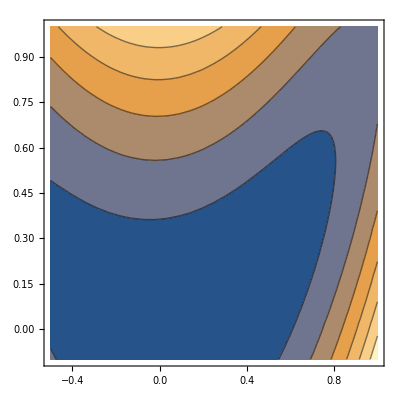
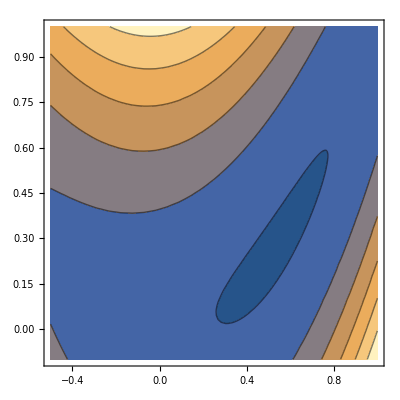
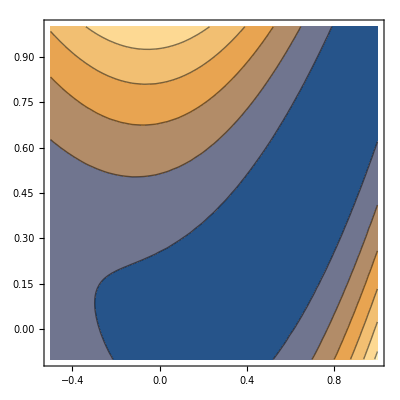
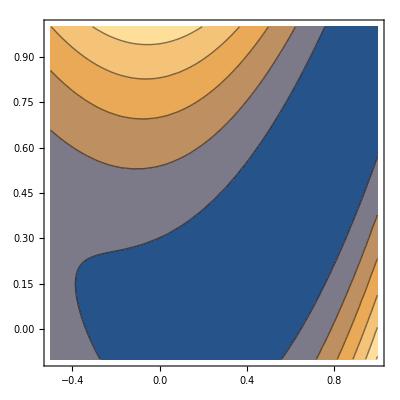
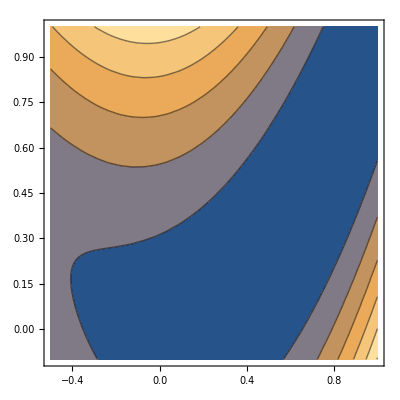
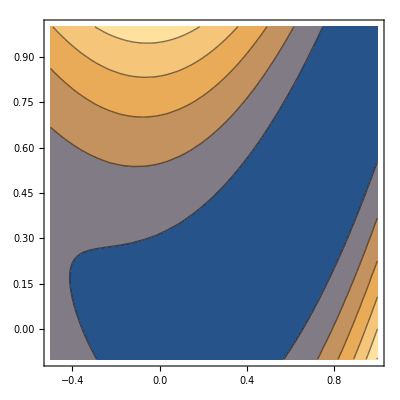
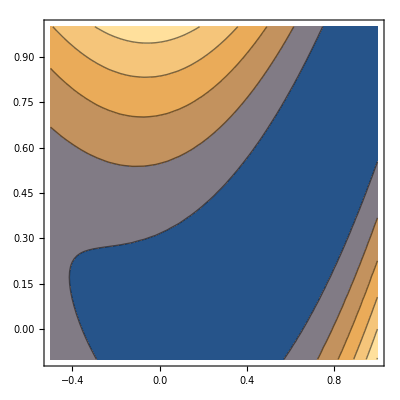

```mathematica
Table[graph[32*4^-i],{i,0,6}]
```

```mathematica
NMinimize[10(x^2-y)^2+(x-1)^2-32/g[x,y],{x,y}]
```

{6.29623,{x→0.135748,y→-0.0238153}}

```mathematica
NMinimize[10(x^2-y)^2+(x-1)^2-16/g[x,y],{x,y}]
```

{3.43126,{x→0.34943,y→0.0964739}}

```mathematica
mins=Table[{x,y}/.NMinimize[10(x^2-y)^2+(x-1)^2-(32*4^-i)/g[x,y],{x,y}][[2]],{i,0,6}]
```

{{0.135748,-0.0238153},{0.530854,0.265761},{0.786486,0.612317},{0.921505,0.847029},{0.97655,0.953025},{0.993782,0.987438},{0.99842,0.996801}}

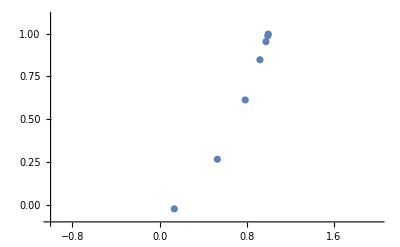

```mathematica
ListPlot[mins,PlotRange->{{-1,2},{-0.1,1.1}},AxesOrigin->{-1,-0.1}]
```

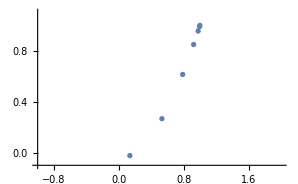
```mathematica
-Graphics--Graphics-
```

Это возвращение назад объясняется тем, что на первой итерации у штрафной функции минимум находится достаточно далеко от точки минимума исходной функции.